```mathematica
f3[x_]:=Graphics[{Line[Apply[Sequence,Table[{n,m},{m,1,x},{n,1,x}],{1}]⟦FindShortestTour[Sequence@@@Table[{n,m},{m,1,x},{n,1,x}]]//Last⟧],PointSize[Small],Red,Point[Apply[Sequence,Table[{n,m},{m,1,x},{n,1,x}],{1}]]}]
```

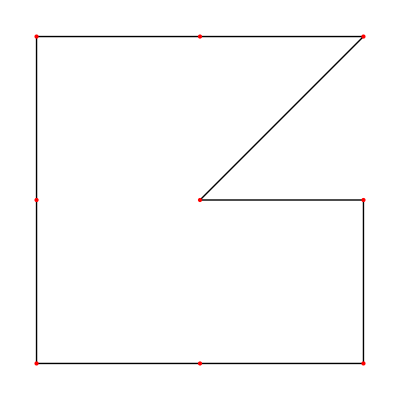

```mathematica
Table[f3[n],{n,3,10}]
```